```mathematica
2-2
```

0

# Spectral Bounds

Nicholas Wheeler
2 September 2011

While browsing in M. Aigner & G. M. Ziegler's Proofs from THE BOOK (1998) this morning—it has for several weeks provided my primary bathroom reading material—I came upon a theorem first obtained by Laguerre, and presented here as a consequence of the inequalities

harmonic mean ⩽ geometric mean ⩽ arithmetic mean

THEOREM: Suppose all roots of the polynomial

x^n+a_(n-1)x^(n-1)+a_(n-2)x^(n-2) ... +a_0

are real. Then the roots are contained in the interval with endpoints

-(a_(n-1))/n± (n-1)/n √((a_(n-1))^2-(2n)/(n-1)a_(n-2))

I am curious to know whether this pretty result permits one to place useful bounds on the spectra of finite-dimensional hermitian (or real symmetric) matrices.

The eigenvalues of a real or complex hermitian matrix are known to be real. The characteristic polynomial of such a matrix 𝔸 can be developed (I quote now from my "Trace of Inverted Matrix" [pdf file: December 1996])

∑_(k=0)^n 1/(k!)Q_k(-x)^(n-k)=Q_0(-x)^n+Q_1(-x)^(n-1)+1/2 Q_2(-x)^(n-2)+⋯

where

Q_0=1
Q_1=T_1
Q_2=T_1^2-T_2
     ⋮

with T_k=Tr[𝔸^k]. To render the polynomial described above into the monic form presumed by the theorem, we divide by (-)^n Q_0=(-)^n, to obtain

x^n-T_1 x^(n-1)+(T_1^2-T_2)/2 x^(n-2)+⋯ ≡x^n+a_(n-1) x^(n-1)+ a_(n-2) x^(n-2)+ ⋯

whence

a_(n-1)=-T_1
a_(n-2)=(T_1^2-T_2)/2

In this notation, the spectral bounds asserted by Laguerre's theorem become, after simplifications,

T_1/n± (n-1)/n √((n T_2-T_1^2)/(n-1))

where n is the dimension of the square matrix 𝔸.

EXPERIMENTAL TESTS: Look first to random matrices that, by the Perron-Frobenius theorem, are expected to have a solitary large eigenvalue. Many runs indicate that the upper Laguerre bound does typically provide a rough estimate of the maximal eigenvalue, but that the lower Laguerre bound is typically very wide of the mark.

```mathematica
𝔸=(𝕄+Transpose[𝕄])/2/.𝕄->RandomReal[{},{10,10}];

Tr[𝔸]/10+ (10-1)/10 √((10Tr[𝔸.𝔸]-Tr[𝔸]^2)/(10-1))
Max[Eigenvalues[𝔸]]
Min[Eigenvalues[𝔸]]
Tr[𝔸]/10- (10-1)/10 √((10Tr[𝔸.𝔸]-Tr[𝔸]^2)/(10-1))
```

5.13635

4.69348

-1.1499

-4.16901

If we give up positivity of the matrix elements we lose the isolated large eigenvalue, but the Laguerre bounds still behave as though it were to be expected:

```mathematica
𝔹=(𝕄+Transpose[𝕄])/2/.𝕄->RandomReal[{-1,1},{10,10}];

Tr[𝔹]/10+ (10-1)/10 √((10Tr[𝔹.𝔹]-Tr[𝔹]^2)/(10-1))
Max[Eigenvalues[𝔹]]
Min[Eigenvalues[𝔹]]
Tr[𝔹]/10- (10-1)/10 √((10Tr[𝔹.𝔹]-Tr[𝔹]^2)/(10-1))
```

3.71434

1.83798

-2.05124

-3.60805

But in all cases the Laguerre bounds do in fact bracket the spectrum; they just don't provide very accurate estimates of its extrema.

### Note added on 25 September

Instead of by-hand repetition of the preceding command we can automatically do so many time, and plot the results…which will serve to expose the regularity of the results. To illustrate the procedure I look again to the case of symmetric 10 × 10 matrices, with elements selected at random from the unit interval:

```mathematica
upper[x_]:=Tr[x]/10+ (10-1)/10 √((10Tr[x.x]-Tr[x]^2)/(10-1))
lower[x_]:=Tr[x]/10- (10-1)/10 √((10Tr[x.x]-Tr[x]^2)/(10-1))
```

```mathematica
SpectralBoundsData=Flatten[Table[{upper[𝔸],lower[𝔸]}/.𝔸->(𝕄+Transpose[𝕄])/2/.𝕄->RandomReal[{},{10,10}],{k,1,1000}]];
```

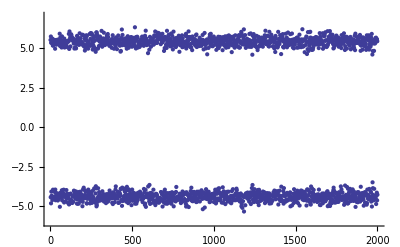

```mathematica
DisplayBounds=ListPlot[SpectralBoundsData,PlotRange->{-6,7}]
```

One could look to the means and variances of the upper/lower bounds, and to how they depend upon  dimension and properties of the statistic that generates the matrix elements. 

Simultaneous display of the following figures

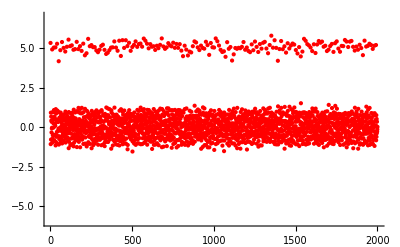

```mathematica
DisplayEigenvalues=ListPlot[Flatten[Table[Eigenvalues[𝔸]/.𝔸->(𝕄+Transpose[𝕄])/2/.𝕄->RandomReal[{},{10,10}],{k,1,200}]], PlotStyle->Red, PlotRange->{-6,7}]
```

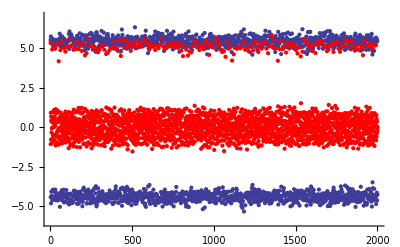

```mathematica
Show[{DisplayBounds, DisplayEigenvalues}]
```

It is interesting that the upper bound does capture—and pretty well approximate—the "exceptionally large leading eigenvalues" dictated by the Perron-Frobenius Theorem.